```mathematica
EulerPhi
adskhld
```

```mathematica
Import["https://www.nps.gov","Images"]
```

Import::htmlimg: Some images could not be imported.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

WolframAlphaQueryResults

from Yue Chinese:  | i love you

```mathematica
Entity["Word","beauty"]
```

```mathematica
EmbedCode[APIFunction[{"x"->"Number"},#x!&,"PNG"],"Java"]
```

URLRead::invhttp: Failed to connect to www.wolframcloud.com port 443: Timed out.

EmbedCode::baddeploy: The CloudDeploy operation failed, therefore EmbedCode cannot operate on the object.

$Failed

[i/2 for i in range(10)]

StartExternalSession::help: For help configuring the Python evaluator, see Configure Python for ExternalEvaluate.

StartExternalSession::noinstall: No valid installations for system Python were found with the options specified.

$Failed

```mathematica
GeoGraphics[Text[Style["Hello!",150]],GeoRange->"World"]
```

-Graphics-

```mathematica
Graphics[Rotate[Rectangle[],30Degree]]
```

-Graphics-

```mathematica
Graphics[{EdgeForm[White],Table[Rotate[Rectangle[],r 5Degree],{r,0,10}]}]
```

-Graphics-

```mathematica
Manipulate[​​
Graphics[
{EdgeForm[White],Table[Rotate[Rectangle[],angle r Degree],{r,0,n}]
}],
{angle,0,45},
{n,1,100,1}
]
```

```mathematica
Manipulate[Graphics[{EdgeForm[White],Table[Scale[Rotate[Rectangle[],angle r Degree],1-r/n],{r,0,n}]}],{angle,0,45},{n,1,100}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[White],Table[Scale[Rotate[Rectangle[],45°],1-x/n],{x,n}]},
Axes->True,
PlotRange->{0,1}
],{n,1,10,1}]
```

```mathematica
Manipulate[Graphics[{EdgeForm[White],Table[Rotate[Scale[Rectangle[],1-x/n],45°],{x,n}]}],{n,1,10,1}]
```

```mathematica
Graphics[{EdgeForm[Pink],
Rectangle[],
Green,Rotate[Rectangle[],45°],
Red,Scale[Rotate[Rectangle[],45°],0.1],
Red,Scale[Rotate[Rectangle[],45°],0.05],
Purple,Rotate[Scale[Rectangle[],0.5],45°],
Opacity[0.5],White, Scale[Rectangle[],0.5]  },
Axes->True,
PlotRange->{{-0.5,1.5},{-0.5,1.5}}
]
```

-Graphics-

```mathematica
Graphics[{
Rectangle[{1,-1}],
Green,Scale[Rectangle[{1,-1}],.5,{Left,Top}],
Scale[Rotate[Rectangle[{1,-1}],45°],.5],
Red,Scale[Rectangle[{1,-1}],.5,{1,0}] ,
Purple,Scale[Rectangle[{1,-1}],0.5] ,
Purple,Scale[Rectangle[{1,-1}],-0.5] 
},
Axes->True,
PlotRange->{{-1,2},{-1,2}},
GridLines->Automatic,
GridLinesStyle->Directive[Gray, Dashed]]
```

-Graphics-

```mathematica
Graphics[{
Rectangle[],Rectangle[{1,1}],
Red,Scale[Rectangle[],.5],Scale[Rectangle[{1,1}],.5] ,

Purple,Rectangle[{1,0}],Rectangle[{0,1}],
Green,Scale[Rectangle[{1,0}],.5],Scale[Rectangle[{0,1}],.5]},
Axes->True,PlotRange->{{0,2},{0,2}}]
```

-Graphics-

```mathematica
Graphics[{
Rectangle[],Rectangle[{1,1} ],
Purple,Rectangle[ {0,1}],Rectangle[{1,0}],
Yellow,Scale[Rectangle[],0.5],Scale[Rectangle[{1,1}],0.5],
Green,Scale[Rectangle[{0,1}],0.5],Scale[Rectangle[{1,0}],0.5]
},Axes->True]
```

-Graphics-

```mathematica
Graphics[{
 Rectangle[{1,0}],
Green, Scale[Rectangle[{1,0}],0.5]
},Axes->True]
```

-Graphics-

```mathematica
Normal@Scale[Rectangle[{1,-1}],.5,{Left,Top}]
```

Scale[Rectangle[{1,-1}],0.5,{Left,Top}]

```mathematica
Dynamic[Manipulate[r=1;circ=ParametricPlot[r{Sin[x],Cos[x]},{x,0,2Pi},PlotStyle->Thick][[1]];
i=r α;j=Pi r;Px=r Sin[α];Py=r Cos[α];vP={Px,Py};
Ex=Px-i Cos[α];Ey=Py+i Sin[α];vE={Ex,Ey};
Fx=Px+(j-i)Cos[α];Fy=Py-(j-i)Sin[α];vF={Fx,Fy};EF=Line[{vE,vF}];
iv={ParametricPlot[r{Sin[v],Cos[v]},{v,0,α},PlotStyle->{Thick,Red}][[1]]};
pP=Point[vP];pE=Point[vE];radius={Dashed,Line[{{0,0},vP}]};
evE={ParametricPlot[r{(Sin[w]-w Cos[w]),(Cos[w]+w Sin[w])},{w,α,0},PlotStyle->{Thick,RGBColor[0.2,0.5,0.2]}][[1]]};
evF={ParametricPlot[r{r Sin[w]+(j-w)Cos[w],r Cos[w]-(j-w)Sin[w]},{w,α,0},PlotStyle->{Thick,RGBColor[0.2,0.5,1]}][[1]]};
vT={Ex-ext Sin[α],Ey-ext Cos[α]};vU={Ex+ext Sin[α],Ey+ext Cos[α]};
TU={Dashed,Line[{vT,vU}]};
Graphics[{TU,evE,If[evFs,evF,{}],EF,circ,iv,pP,pE,radius},ImageSize->{450,400},Axes->True,PlotRange->{{-r,r+2.4},{-r-1,r+1}}],{{α,2,"roll line on circle"},0.01,Pi},{{ext,1,"length of tangent line"},0.1,2},{{evFs,False,"show other curve"},{True,False}},TrackedSymbols->Manipulate]]
```

```mathematica
α=Entity["PlaneCurve","Circle"]["ParametricEquations"][1][t];
invc=ResourceFunction["InvoluteCurve"][α,t]//Simplify
```

{Cos[t]+t Sin[t],-t Cos[t]+Sin[t]}

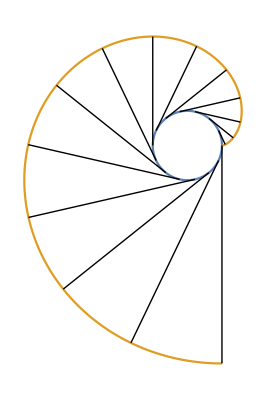

```mathematica
z[k_]:=Line[{α,invc}/. t->(π k)/7]
ParametricPlot[Evaluate[{α,invc}],{t,0,2 π},Epilog->Array[z,14],Axes->False]
```

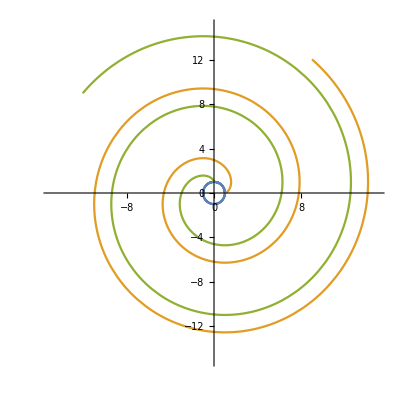

```mathematica
p=15;
ParametricPlot[Evaluate[{α,invc,ResourceFunction["InvoluteCurve"][α/. t->t+π/2,t]}],{t,0,p},PlotRange->{{-p,p},{-p,p}}]
```

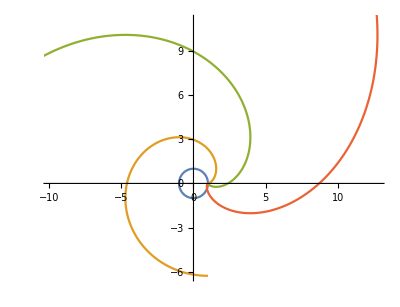

```mathematica
ParametricPlot[Evaluate[NestList[ResourceFunction["InvoluteCurve"][#,t]&,α,3]],{t,0.01,2 π}]
```

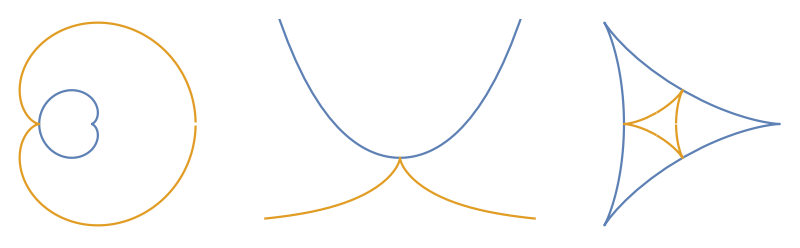

```mathematica
InvoluteCurvePlot[c_,{t_,t0_,tf_},opts___]:=ParametricPlot[Evaluate[{c,ResourceFunction["InvoluteCurve"][c,t]}],{t,t0,tf},opts,Axes->False];
GraphicsRow[{InvoluteCurvePlot[Entity["PlaneCurve","Cardioid"]["ParametricEquations"][1][t],{t,0.01,2 π-.01}],InvoluteCurvePlot[Entity["PlaneCurve","Catenary"]["ParametricEquations"][1][t],{t,-3,3},PlotRange->{{-2,2},{0,3}}],InvoluteCurvePlot[Entity["PlaneCurve","Deltoid"]["ParametricEquations"][1][t],{t,0.01,2 π-.01}]}]
```

```mathematica
x=Function[{r,a,t},(r+(r/(a^2-1))Sin[a t])Cos[t] -a(r/(a^2-1)) Cos[a t]Sin[t]];
y=Function[{r,a,t},(r+(r/(a^2-1))Sin[a t])Sin[t] + a(r/(a^2-1))Cos[a t]Cos[t]];
```

```mathematica
Manipulate[
Module[{r=.5,d=1.8,points1,points2,curve1points,curve2points,centerpoints},

points1=Table[{r*theta+x[r,a1,t]*Cos[theta]+y[r,a1,t]*Sin[theta],
-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta] + y[r,a1,t]*Cos[theta]-x[r,a1,t]*Sin[theta]},{t,0,2*Pi,Pi/32}]; 
points2=Table[{d+r*theta+x[r,a2,t]*Cos[Pi+theta]+y[r,a2,t]*Sin[Pi+theta],
-y[r,a2,Pi/2+theta]*Cos[Pi+theta]+x[r,a2,Pi/2+theta]*Sin[Pi+theta] + y[r,a2,t]*Cos[Pi+theta]-x[r,a2,t]*Sin[Pi+theta]},{t,0,2*Pi,Pi/32}]; 
curve1points=Table[{r*theta+x[r,a1,3Pi/2]*Cos[theta]+y[r,a1,3Pi/2]*Sin[theta],
-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta] + y[r,a1,3Pi/2]*Cos[theta]-x[r,a1,3Pi/2]*Sin[theta]},{theta,-Pi,3*Pi,Pi/32}];
curve2points=Table[{r*theta+x[r,a1,Pi/2]*Cos[theta]+y[r,a1,Pi/2]*Sin[theta],
-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta] + y[r,a1,Pi/2]*Cos[theta]-x[r,a1,Pi/2]*Sin[theta]},{theta,-Pi/2,3*Pi,Pi/32}];
centerpoints=Table[{r*theta,
-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta] },{theta,-Pi,3*Pi,Pi/32}];
Graphics[{
RGBColor[1,0,0],
Line[centerpoints[[1;;Round[32*theta/Pi+33]]]],
RGBColor[1,0,1],
Line[curve1points[[1;;Round[32*theta/Pi+33]]]],
RGBColor[0,1,1],
Line[curve2points[[1;;Round[32*theta/Pi+17]]]],
RGBColor[0,0,1],
Thickness[.005],
Line[points1],
Line[points2],
Thickness[.001],
Table[Line[{{r*theta,-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta]},points1[[k]]}],{k,1,Length[points1],2}],
Table[Line[{{d+r*theta,-y[r,a2,Pi/2+theta]*Cos[Pi+theta]+x[r,a2,Pi/2+theta]*Sin[Pi+theta]},points2[[k]]}],{k,1,Length[points2],2}],
PointSize[.005],
RGBColor[1,0,1],
Point[{r*theta+x[r,a1,3Pi/2]*Cos[theta]+y[r,a1,3Pi/2]*Sin[theta],
-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta] + y[r,a1,3Pi/2]*Cos[theta]-x[r,a1,3Pi/2]*Sin[theta]}],
RGBColor[0,1,1],
Point[{r*theta+x[r,a1,Pi/2]*Cos[theta]+y[r,a1,Pi/2]*Sin[theta],
-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta] + y[r,a1,Pi/2]*Cos[theta]-x[r,a1,Pi/2]*Sin[theta]}],
RGBColor[0,0,0],
Thickness[.01],
Line[{{-r-.1,-.01},{3*Pi*r+d+r+.1,-.01}}],
Line[{{d+r*theta-r+.1,2*r+.2},{d+r*theta-.1,r}}],
Line[{{r*theta+r+.2,r},{r*theta+r,2*r+.2}}],
Line[{{r*theta+r+.2,r},{d+r*theta-r+.1,2*r+.2}}],
Line[{{d+r*theta-r+.1,2*r+.2},{r*theta+r+.1,2*r}}],
Line[{{r*theta+r-.1,2*r+.2},{r*theta+r+.1,2*r+.2}}],
Line[{{r*theta+.2,2*r},{r*theta-.2,2*r}}],
Line[{{d+r*theta-.2,2*r},{d+r*theta+.2,2*r}}],
Line[{{r*theta+r+.2-.15*Cos[2*(.5+theta)],r+.15*Sin[2*(.5+theta)]},{r*theta+r+.2-.15*Cos[2*(.5+theta)]+.1,r+.15*Sin[2*(.5+theta)]}}],
Line[{{r*theta+r+.2+.15*Cos[2*(.5+theta)],r-.15*Sin[2*(.5+theta)]},{r*theta+r+.2+.15*Cos[2*(.5+theta)]+.1,r-.15*Sin[2*(.5+theta)]}}],
Thickness[.005],
Line[{{r*theta+.2,2*r},{r*theta+r+.1,2*r}}],
Line[{{r*theta,2*r},{r*theta+r+.2,r}}],
Line[{{r*theta,-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta]},{r*theta+r+.2,r}}],
Line[{{d+r*theta-.1,r},{d+r*theta,-y[r,a2,Pi/2+theta]*Cos[Pi+theta]+x[r,a2,Pi/2+theta]*Sin[Pi+theta]}}],
Line[{{d+r*theta-r+.2,2*r}, {d+r*theta-.2,2*r}}],
Line[{{d+r*theta-.1,r},{d+r*theta,2*r}}],
Line[{{r*theta+r+.2,r},{r*theta+r+.2-.15*Cos[2*(.5+theta)],r+.15*Sin[2*(.5+theta)]}}],
Line[{{r*theta+r+.2,r},{r*theta+r+.2+.15*Cos[2*(.5+theta)],r-.15*Sin[2*(.5+theta)]}}],
Line[{{d+r*theta-r+.1,2*r+.2},{d+r*theta-r+.1,2*r+.3}}],
Line[{{d+r*theta-r+.1,2*r+.3},{d+r*theta-r,2*r+.4}}],
Line[{{d+r*theta-r+.1,2*r+.3},{d+r*theta-r+.2,2*r+.4}}],
Line[{{d+r*theta-r,2*r+.4},{d+r*theta-r-.2,2*r+.4}}],
Line[{{d+r*theta-r+.2,2*r+.4},{d+r*theta-r+.4,2*r+.4}}],
PointSize[.02],
Point[{r*theta,-y[r,a1,3Pi/2+theta]*Cos[theta]+x[r,a1,3Pi/2+theta]*Sin[theta]}],
Point[{d+r*theta,-y[r,a2,Pi/2+theta]*Cos[Pi+theta]+x[r,a2,Pi/2+theta]*Sin[Pi+theta]}]
},Axes->{True,False},Ticks->None,PlotRange->{{-r-.1, 2*Pi*r+d+r+.1},{0,2*r+1}},ImageSize->{600,300}]
],
Row[{Spacer[40],Control@{{theta,0,"time"},0,2*3.1416,.0001,Appearance->"Labeled"}}],
Row[{
Control@{{a1,3,"back wheel sides"},Range[3,9,2]},
Spacer[20],
Control@{{a2,5,"front wheel sides"},Range[3,9,2]}
}],
SaveDefinitions->True]
```